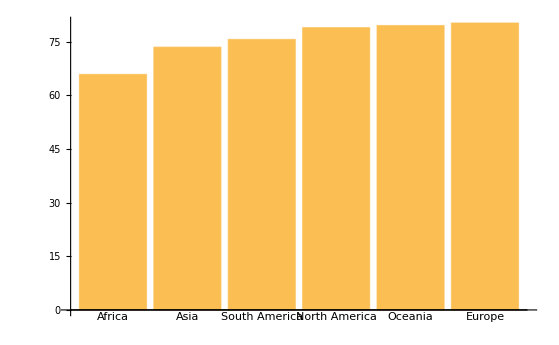

```mathematica
data=(
CountryData[]
// Select[(CountryData[#,"LifeExpectancy"]//MissingQ // Not)&]
 // Map[<|
	"continent"->CountryData[#, "Continent"],
	"population" -> CountryData[#,"Population"],
	"populationYears"->CountryData[#,"Population"]*CountryData[#, "LifeExpectancy"]
|>&]
   //Dataset
);
averageLifeExpectancyByContinent=(
data [GroupBy["continent"], Total]
[All,<|"averageLifeExpectancy"->#populationYears/#population|>&]
  [SortBy["averageLifeExpectancy"]]
);
BarChart[Normal[averageLifeExpectancyByContinent[All, "averageLifeExpectancy"]],
ChartLabels->Normal[averageLifeExpectancyByContinent[Keys]]]
```